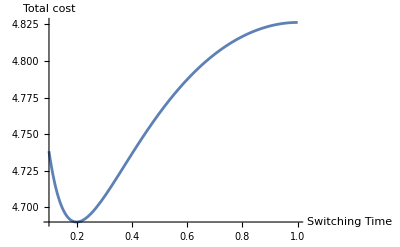

```mathematica
r=1;                   (*Must be numeric*)
q1s=0.3;               (*Initial condition for q1*)
q2s=0.1;               (*Initial condition for q2*)
beta  = 2;
alphaFun[t_,tSw_]:=Piecewise[{{0,t<tSw},(*alpha=0 if t<tSwitch*){1/2,t>=tSw}   (*alpha=1/2 otherwise*)}];
cost[q1_,q2_]:=1/(q1*q2)

totalCost[tSwitch_]:=Module[{},
{q1Sol,q2Sol}=NDSolveValue[{
q1'[t]==r*alphaFun[t,tSwitch],q2'[t]==r*(1-alphaFun[t,tSwitch]),
q1[0]==q1s,
q2[0]==q2s},
{q1,q2},{t,0,1}];
p1 = Plot[{q1Sol[t],q2Sol[t]},{t,0,1},PlotLegends->{"q1(t)","q2(t)"}, AxesLabel->{"Investment time", "AI Quality"}];
p2 = Plot[cost[q1Sol[t], q2Sol[t]], {t,0,1}]; 
tc = NIntegrate[Exp[-beta t]*cost[q1Sol[t],q2Sol[t]],{t,0,1}];
{p1,tc, p2}
]
Plot[totalCost[ts][[2]], {ts, .1, 1}, AxesLabel->{"Switching Time", "Total cost"}]
```

```mathematica
totalCost[.1][[2]]
```

4.73821

{4.82641,{ts→0}}

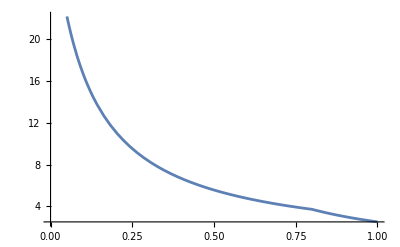

```mathematica
totalCost[0.8][[3]]
```

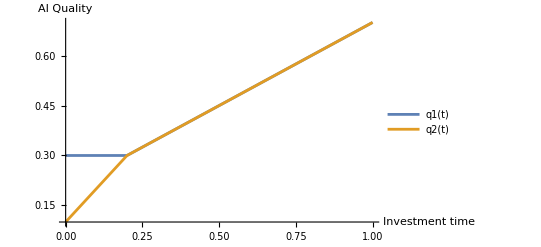

```mathematica
totalCost[0.2][[1]]
```

```mathematica
cost[q1_,q2_]:=1/q1*q2
beta = 1
```

1

```mathematica
ClearAll[costFunction];
costFunction[tSw_?NumericQ]:=Module[{q1Sol,q2Sol,(*the numerical solution for q1,q2*)costVal       (*the numeric value of the integral*)},(*Solve the ODE system under the given tSw*){q1Sol,q2Sol}=NDSolveValue[{q1'[t]==r*Piecewise[{{0,t<tSw},{1/2,t>=tSw}}],q2'[t]==r*(1-Piecewise[{{0,t<tSw},{1/2,t>=tSw}}]),q1[0]==q1s,q2[0]==q2s},{q1,q2},{t,0,1}];
(*Define cost at time t*)With[{cost=1/(q1Sol[t]*q2Sol[t])},(*Compute total cost=∫exp(-beta t) cost dt,from t=0 to 1*)costVal=NIntegrate[Exp[-beta t]*cost,{t,0,1}];];
(*Return that costVal*)costVal];
sol=NMinimize[{costFunction[tSw],0<=tSw<=1},{tSw}];
sol
```

{4.68976,{tSw→0.2}}

```mathematica
sol
```

{4.68976,{tSw→0.2}}

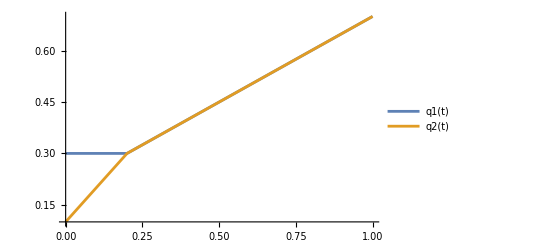

```mathematica
totalCost[0.2][[1]]
```